Ananye Patel
UID: 404808384
ananye.97@gmail.com
PHYSICS 105A Mathematica HW 2

```mathematica
Remove["Global`*"];
(* Problem 1 *)
Print["The solution x[t] given the conditions x''[t]==a, x'[0]==v0, x[0]==x0 is: "];
Print[DSolve[{x''[t]==a,x[0]==x0,x'[0]==v0},x[t],t]];
```

The solution x[t] given the conditions x''[t]==a, x'[0]==v0, x[0]==x0 is:

{{x[t]→1/2 (a t^2+2 t v0+2 x0)}}

x[t]→{1/2 (a t^2+2 t v0+2 x0)}

{{x[t]→2+5 t+5 t^2}}

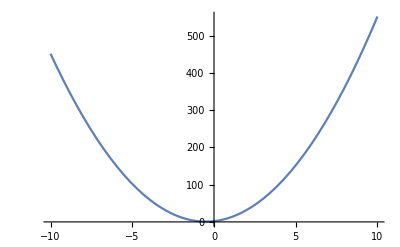

```mathematica
x[t]->{(1/2)(a t^2+2 t v0+2 x0)}
soln=DSolve[{x''[t]==10,x[0]==2,x'[0]==5},x[t],t]
Plot[x[t]/.soln,{t,-10,10}]
```

```mathematica
Remove["Global`*"];
(* Problem 2 *)
eqnlist={m*Subscript[x, 1]''[t]==k*Subscript[x, 2][t]-2*k*Subscript[x, 1][t],m*Subscript[x, 2]''[t]==k*Subscript[x, 1][t]-2*k*Subscript[x, 2][t],Subscript[x, 1]'[0]==0,Subscript[x, 2]'[0]==0,Subscript[x, 1][0]==0,Subscript[x, 2][0]==L};
Print["The solutions x_1[t] and x_2[t] to the DEs given the initial conditions x_1'[0]=0, x_2'[0]=0, x_1[0]=0, x_2[0]=L are: "];
Print[soln=DSolve[eqnlist,{Subscript[x, 1][t],Subscript[x, 2][t]},t]];
```

The solutions x_1[t] and x_2[t] to the DEs given the initial conditions x_1'[0]=0, x_2'[0]=0, x_1[0]=0, x_2[0]=L are:

{{x_1[t]→-1/4 ⅇ^(-(ⅈ √k t)/(√m)-(ⅈ √3 √k t)/(√m)) (ⅇ^((ⅈ √k t)/(√m))-ⅇ^((ⅈ √3 √k t)/(√m))-ⅇ^((2 ⅈ √k t)/(√m)+(ⅈ √3 √k t)/(√m))+ⅇ^((ⅈ √k t)/(√m)+(2 ⅈ √3 √k t)/(√m))) L,x_2[t]→1/4 ⅇ^(-(ⅈ √k t)/(√m)-(ⅈ √3 √k t)/(√m)) (ⅇ^((ⅈ √k t)/(√m))+ⅇ^((ⅈ √3 √k t)/(√m))+ⅇ^((2 ⅈ √k t)/(√m)+(ⅈ √3 √k t)/(√m))+ⅇ^((ⅈ √k t)/(√m)+(2 ⅈ √3 √k t)/(√m))) L}}

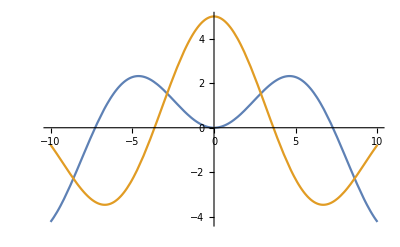

```mathematica
m=3;k=0.3;L=5;
Plot[Evaluate[{Subscript[x, 1][t],Subscript[x, 2][t]}/.soln],{t,-10,10}]
```

{{x[t]→1/(2 √(β^2-ω_0^2))A_0 (-ⅇ^(t (-β-√(β^2-ω_0^2))) β+ⅇ^(t (-β+√(β^2-ω_0^2))) β+ⅇ^(t (-β-√(β^2-ω_0^2))) √(β^2-ω_0^2)+ⅇ^(t (-β+√(β^2-ω_0^2))) √(β^2-ω_0^2))}}

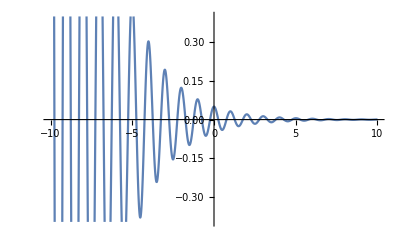

-Graphics-

ReplaceAll::reps: {{{x[-9.99959]→-6.23266×10^52}}[(5 π)/2,-9.99959]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x[-9.99959]→-6.23266×10^52}}[7.85398,-9.99959]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{{x[-9.59143]→-3.69079×10^50}}[(5 π)/2,-9.59143]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

```mathematica
Remove["Global`*"];
(* Problem 3 *)
deqn={x''[t]==-2*β*x'[t]-((Subscript[ω, 0])^2)*x[t],x[0]==Subscript[A, 0],x'[0]==0};
sol=DSolve[deqn,{x[t]},t]
Subscript[A, 0]:=0.05;Subscript[ω, 0]:=2*Pi;β:=Pi/7;
Plot[x[t]/.sol,{t,-10,10}]
Subscript[A, 0]:=0.05;Subscript[ω, 0]:=2*Pi;β:=5*Pi/2;
Plot[x[t]/.sol,{t,-10,10}]
Subscript[A, 0]:=0.05;
plot=x[t]/.Subscript[ω, 0]->2*Pi/.β->2*Pi;
traj[β_]=Plot[plot/.sol[β,t],{t,-10,10},PlotRange->{{-10,10},{-10,10}},AxesLabel->{"t","x"}]
Manipulate[traj[β],{β,0,4*Pi}]
```

{x[t]→1/(2 √(-β^2+ω_0^2))A (ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β-ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β+ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) √(-β^2+ω_0^2)+ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) √(-β^2+ω_0^2))}

{x[t]→1/(2 τ_0 ω_0^4 √(-β^2+ω_0^2))(2 ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2-2 ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2-ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-ⅈ A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-4 a f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a f t ω_0^2 √(-β^2+ω_0^2)+A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2)+A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2))}

{x[t]→1/(2 τ_0 ω_0^4 √(-β^2+ω_0^2))(-2 ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2+2 ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2+2 ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2-2 ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2+ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β τ_0 ω_0^2+ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β τ_0 ω_0^2+ⅈ A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-ⅈ A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4+4 f β √(-β^2+ω_0^2)-4 a f β √(-β^2+ω_0^2)-2 ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)-2 ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)-2 f t ω_0^2 √(-β^2+ω_0^2)+2 a f t ω_0^2 √(-β^2+ω_0^2)+2 f τ_0 ω_0^2 √(-β^2+ω_0^2)-ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f τ_0 ω_0^2 √(-β^2+ω_0^2)-ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f τ_0 ω_0^2 √(-β^2+ω_0^2)+A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2)+A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2))}

For the undriven time interval, the solution to the equations of motion is: x[t]→1/(2 √(-β^2+ω_0^2))A (ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β-ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β+ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) √(-β^2+ω_0^2)+ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) √(-β^2+ω_0^2))

For the driven time interval, the solution to the equations of motion is: x[t]→1/(2 τ_0 ω_0^4 √(-β^2+ω_0^2))(2 ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2-2 ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2-ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-ⅈ A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-4 a f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a f t ω_0^2 √(-β^2+ω_0^2)+A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2)+A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2))

For the driven time interval, the solution to the equations of motion is: x[t]→1/(2 τ_0 ω_0^4 √(-β^2+ω_0^2))(-2 ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2+2 ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β^2+2 ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2-2 ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β^2+ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2+ⅈ a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f ω_0^2-ⅈ ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β τ_0 ω_0^2+ⅈ ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β τ_0 ω_0^2+ⅈ A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4-ⅈ A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) β τ_0 ω_0^4+4 f β √(-β^2+ω_0^2)-4 a f β √(-β^2+ω_0^2)-2 ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)-2 ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)+2 a ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f β √(-β^2+ω_0^2)-2 f t ω_0^2 √(-β^2+ω_0^2)+2 a f t ω_0^2 √(-β^2+ω_0^2)+2 f τ_0 ω_0^2 √(-β^2+ω_0^2)-ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) f τ_0 ω_0^2 √(-β^2+ω_0^2)-ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) f τ_0 ω_0^2 √(-β^2+ω_0^2)+A ⅇ^(t (-β-ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2)+A ⅇ^(t (-β+ⅈ √(-β^2+ω_0^2))) τ_0 ω_0^4 √(-β^2+ω_0^2))

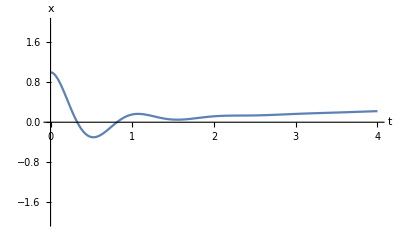

```mathematica
(* Problem 4 *)
Remove["Global`*"];
debug=True;
$Assumptions={Element[{Subscript[ω, 0],β},Reals] && (β^2)<(Subscript[ω, 0]^2)};

(* Part i *)
(* Solving the DE for the interval t<0 *)
oscillations[β_,t_]=x''[t]+2*β*x'[t]+(Subscript[ω, 0]^2)*x[t]==0;
ic={x[0]==A,x'[0]==0};
eqnlist=Append[ic,oscillations[β,t]];
soln1[β_,t_]=DSolve[eqnlist, x[t],t][[1]]

(* Solving the DE for the interval 0<t<Subscript[τ, 0] *)
oscillations[β_,t_]=x''[t]+2*β*x'[t]+(Subscript[ω, 0]^2)*x[t]==(f*a*t)/(Subscript[τ, 0]);
ic={x[0]==A,x'[0]==0};
eqnlist=Append[ic,oscillations[β,t]];
soln2[β_,t_]=DSolve[eqnlist, x[t],t][[1]]

(* Solving the DE for the interval t>Subscript[τ, 0] *)
oscillations[β_,t_]=x''[t]+2*β*x'[t]+(Subscript[ω, 0]^2)*x[t]==((f*a*t)/(Subscript[τ, 0]))-((f*(t-Subscript[τ, 0]))/Subscript[τ, 0]);
ic={x[0]==A,x'[0]==0};
eqnlist=Append[ic,oscillations[β,t]];
soln3[β_,t_]=DSolve[eqnlist, x[t],t][[1]]

Print["For the undriven time interval, the solution to the equations of motion is: x[t]→",x[t]/.soln1[β,t]]
Print["For the driven time interval, the solution to the equations of motion is: x[t]→",x[t]/.soln2[β,t]]
Print["For the driven time interval, the solution to the equations of motion is: x[t]→",x[t]/.soln3[β,t]]

(* Part ii *)
A=1;Subscript[τ, 0]=1;β=Subscript[ω, 0]/3;a=12;f=0.2;Subscript[ω, 0]=2*Pi;
Plot[x[t]/.soln3[β,t],{t,0,4},PlotRange->{{0,4},{-2,2}},AxesLabel->{"t","x"}]
```